## Poiseuille flow R-R

```mathematica
ClearAll["Global`*"];
```

### For n=2

```mathematica
eq1=a2+b2+(4/63)*S^2;
eq2=A2+B2+C2+D2;
eq3=(2*a2+4*b2+4+(24/63)*S^2)-(2*A2+4*B2-C2+D2);
eq4=(-2*A2+4*B2+4*C2-2*D2)-μ*(-2*(a2-2)+4*(b2+2)+(72/63)*S^2)+Subscript[Ma, T]*(-2*(α1+β1))+Subscript[Ma, γ]*(-2*(2*A2+4*B2-C2+D2));
```

```mathematica
Solve[eq1==0 &&eq2==0&&eq3==0&&eq4==0,{a2,b2,C2,D2}]//FullSimplify
```

{{a2→1/126 (252+8 S^2+(-189 (A2+5 B2)+32 S^2 μ+126 (α1+β1) Ma_T)/(3+3 μ+2 Ma_γ)),b2→1/126 (-4 (63+4 S^2)+(189 (A2+5 B2)-32 S^2 μ-126 (α1+β1) Ma_T)/(3+3 μ+2 Ma_γ)),C2→1/2 (A2+3 B2)+(-189 (A2+5 B2)+32 S^2 μ+126 (α1+β1) Ma_T)/(126 (3+3 μ+2 Ma_γ)),D2→-(378 A2+567 A2 μ+945 B2 μ+32 S^2 μ+126 (α1+β1) Ma_T+126 (3 A2+5 B2) Ma_γ)/(126 (3+3 μ+2 Ma_γ))}}

### For n=3

```mathematica
eq5=a3+b3+(4/21)*S;
eq6=A3+B3+C3+D3;
eq7=(3*a3+5*(b3+(4/21)*S))-(3*A3+5*B3-2*C3);
eq8=(10*B3+10*C3)-μ*(10*(b3+4/21*S))+Subscript[Ma, T]*(-6*(α2+β2))+Subscript[Ma, γ]*(-6*(3*A3+5*B3-2*C3));
```

```mathematica
Solve[eq5==0 &&eq6==0&&eq7==0&&eq8==0,{a3,b3,C3,D3}]//FullSimplify
```

{{a3→(-5 (3 A3+7 B3)+6 (α2+β2) Ma_T)/(2 (5+5 μ+6 Ma_γ)),b3→-(4 S)/21+(5 (3 A3+7 B3)-6 (α2+β2) Ma_T)/(2 (5+5 μ+6 Ma_γ)),C3→(15 A3 μ+5 B3 (-2+5 μ)+6 (α2+β2) Ma_T+6 (3 A3+5 B3) Ma_γ)/(2 (5+5 μ+6 Ma_γ)),D3→-(35 B3 μ+5 A3 (2+5 μ)+6 (α2+β2) Ma_T+6 (5 A3+7 B3) Ma_γ)/(2 (5+5 μ+6 Ma_γ))}}

### For n>3

```mathematica
eq9=an+bn;
eq10=An+Bn+Cn+Dn;
eq11=(n*an+(n+2)*bn)-(n*An+(n+2)*Bn+(-n+1)*Cn+(-n+3)*Dn);
eq12=(n*(n-3)*An+(n+2)*(n-1)*Bn+(-n+1)*(-n-2)*Cn+(-n)*(-n+3)*Dn)-μ*(n*(n-3)*an+(n+2)*(n-1)*bn)+Subscript[Ma, T]*(-n*(n-1)*(αn1+βn1))+Subscript[Ma, γ]*(-n*(n-1)*(n*An+(n+2)*Bn+(-n+1)*Cn+(-n+3)*Dn));
```

```mathematica
Solve[eq9==0 &&eq10==0&&eq11==0&&eq12==0,{an,bn,Cn,Dn}]//FullSimplify
```

{{an→(-3 An+Bn+8 An n-4 (An+Bn) n^2+(-1+n) n (αn1+βn1) Ma_T)/(2 (-1+2 n) (1+μ)+2 (-1+n) n Ma_γ),bn→((-1+2 n) (-3 An+Bn+2 (An+Bn) n)-(-1+n) n (αn1+βn1) Ma_T)/(2 (-1+2 n) (1+μ)+2 (-1+n) n Ma_γ),Cn→((-1+2 n) (-2 Bn+(-3 An-Bn+2 (An+Bn) n) μ)+(-1+n) n ((αn1+βn1) Ma_T+(-3 An-Bn+2 (An+Bn) n) Ma_γ))/(2 (-1+2 n) (1+μ)+2 (-1+n) n Ma_γ),Dn→(-(-1+2 n) (2 An+(-An+Bn+2 (An+Bn) n) μ)+(-1+n) n (-(αn1+βn1) Ma_T-(-An+Bn+2 (An+Bn) n) Ma_γ))/(2 (-1+2 n) (1+μ)+2 (-1+n) n Ma_γ)}}

### Drag

```mathematica
D2=-(378 A2+567 A2 μ+945 B2 μ+32 S^2 μ+126 (α1+β1) Subscript[Ma, T]+126 (3 A2+5 B2) Subscript[Ma, γ])/(126 (3+3 μ+2 Subscript[Ma, γ]));
```

```mathematica
Drag=4*Pi*D2
```

-(2 π (378 A2+567 A2 μ+945 B2 μ+32 S^2 μ+126 (α1+β1) Ma_T+126 (3 A2+5 B2) Ma_γ))/(63 (3+3 μ+2 Ma_γ))

```mathematica
D1=Drag/.{A2-> (1-Uz),B2-> -2/(5*R0^2), α1-> G,β1-> ((1-κ)/(κ+2))*G}
```

-(2 π (378 (1-Uz)-(378 μ)/R0^2+32 S^2 μ+567 (1-Uz) μ+126 (G+(G (1-κ))/(2+κ)) Ma_T+126 (-2/R0^2+3 (1-Uz)) Ma_γ))/(63 (3+3 μ+2 Ma_γ))

```mathematica
Collect[D1,{1-Uz}]//Simplify
```

(2 π (-378 G R0^2 Ma_T+(2+κ) (378 μ+R0^2 (-378-567 μ-32 S^2 μ+189 Uz (2+3 μ))+126 (2+3 R0^2 (-1+Uz)) Ma_γ)))/(63 R0^2 (2+κ) (3+3 μ+2 Ma_γ))

```mathematica
MigU=Solve[D1==0,Uz]//Simplify
```

{{Uz→(378 G R0^2 Ma_T+(2+κ) (-378 μ+R0^2 (378+567 μ+32 S^2 μ)+126 (-2+3 R0^2) Ma_γ))/(189 R0^2 (2+κ) (2+3 μ+2 Ma_γ))}}

```mathematica
MigU=(378 G R0^2 Subscript[Ma, T]+(2+κ) (-378 μ+R0^2 (378+567 μ+32 S^2 μ)+126 (-2+3 R0^2) Subscript[Ma, γ]))/(189 R0^2 (2+κ) (2+3 μ+2 Subscript[Ma, γ]))//Simplify
```

(378 G R0^2 Ma_T+(2+κ) (-378 μ+R0^2 (378+567 μ+32 S^2 μ)+126 (-2+3 R0^2) Ma_γ))/(189 R0^2 (2+κ) (2+3 μ+2 Ma_γ))

```mathematica
Solve[MigU==0,Subscript[Ma, T]]
```

{{Ma_T→-((2+κ) (378 R0^2-378 μ+567 R0^2 μ+32 R0^2 S^2 μ-252 Ma_γ+378 R0^2 Ma_γ))/(378 G R0^2)}}

```mathematica
Limit[MigU,{μ-> Infinity}]
```

(-756+1134 R0^2+64 R0^2 S^2-378 κ+567 R0^2 κ+32 R0^2 S^2 κ)/(1134 R0^2+567 R0^2 κ)

#### Newtonian Fluid sphere limit

```mathematica
Limit[-(2 π (378 +32 S^2 μ+567  μ-126 (G+(G (1-κ))/(2+κ)) Subscript[Ma, T]-378  Subscript[Ma, γ]))/(63 (3+3 μ-2 Subscript[Ma, γ])),{S-> 0,Subscript[Ma, T]-> 0,Subscript[Ma, γ]-> 0}]//Simplify
```

-(2 π (2+3 μ))/(1+μ)

#### Reiner-Rivlin Fluid sphere limit

```mathematica
Limit[-(2 π (378 +32 S^2 μ+567  μ-126 (G+(G (1-κ))/(2+κ)) Subscript[Ma, T]-378  Subscript[Ma, γ]))/(63 (3+3 μ-2 Subscript[Ma, γ])),{Subscript[Ma, T]-> 0,Subscript[Ma, γ]-> 0}]//Simplify
```

-(2 π (378+(567+32 S^2) μ))/(189 (1+μ))

```mathematica
MigU=(-378 G Subscript[Ma, T]+(2+κ) (378+567 μ+32 S^2 μ-378 Subscript[Ma, γ]))/(189 (2+κ) (2+3 μ-2 Subscript[Ma, γ]));
```

```mathematica
MigFD=Limit[MigU,{S-> 0,Subscript[Ma, T]-> 0,Subscript[Ma, γ]-> 0}]//Simplify
```

1

### Flow field

### Flow field in Body Frame

```mathematica
a2=1/126 (252+8 S^2+(-189 (A2+5 B2)+32 S^2 μ+126 (α1+β1) Subscript[Ma, T])/(3+3 μ+2 Subscript[Ma, γ]));b2=1/126 (-4 (63+4 S^2)+(189 (A2+5 B2)-32 S^2 μ-126 (α1+β1) Subscript[Ma, T])/(3+3 μ+2 Subscript[Ma, γ]));C2=1/2 (A2+3 B2)+(-189 (A2+5 B2)+32 S^2 μ+126 (α1+β1) Subscript[Ma, T])/(126 (3+3 μ+2 Subscript[Ma, γ]));D2=-(378 A2+567 A2 μ+945 B2 μ+32 S^2 μ+126 (α1+β1) Subscript[Ma, T]+126 (3 A2+5 B2) Subscript[Ma, γ])/(126 (3+3 μ+2 Subscript[Ma, γ]));
```

```mathematica
ψ1=FullSimplify[((a2-2)*r^2+(b2+2)*r^4+(4/63)*(S^2*r^6))*(0.5*(Sin[θ])^2)];
ψ2=FullSimplify[(A2*r^2+B2*r^4+(C2/r)+(D2*r))*(0.5*(Sin[θ])^2)];
```

```mathematica
uer=-(1/(r^2*Sin[θ]))*D[ψ2,θ];
ueth=(1/(r*Sin[θ]))*D[ψ2,r];
uir=-(1/(r^2*Sin[θ]))*D[ψ1,θ];
uith=(1/(r*Sin[θ]))*D[ψ1,r];
```

```mathematica
ver=FullSimplify[uer]/.{A2-> 1,B2-> -2/(5*R0^2),α1-> G,β1-> ((1-κ)/(2+κ))*G};
veth=FullSimplify[ueth]/.{A2-> 1,B2-> -2/(5*R0^2),α1-> G,β1-> ((1-κ)/(2+κ))*G};
vir=FullSimplify[uir]/.{A2-> 1,B2-> -2/(5*R0^2),α1-> G,β1-> ((1-κ)/(2+κ))*G};
vith=FullSimplify[uith]/.{A2-> 1,B2-> -2/(5*R0^2),α1-> G,β1-> ((1-κ)/(2+κ))*G};
```

```mathematica
{vxe,vye}=TransformedField["Polar"-> "Cartesian",{ver,veth},{r,θ}-> {x,y}]/.{μ->2,S->0,G-> -1,κ-> 1,Subscript[Ma, T]-> 1,Subscript[Ma, γ]-> 1,R0-> 5};
{vxi,vyi}=TransformedField["Polar"-> "Cartesian",{vir,vith},{r,θ}-> {x,y}]/.{μ-> 2,S->0,G-> -1,κ-> 1,Subscript[Ma, T]-> 1,Subscript[Ma, γ]-> 1,R0-> 5};
```

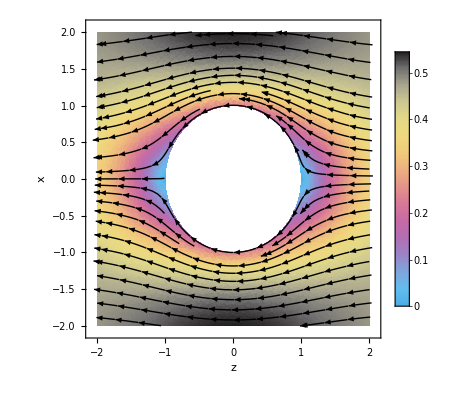

```mathematica
region1=ImplicitRegion[x^2+y^2≥ 1&&-2≤ x≤ 2 && -2≤ y≤ 2,{x,y}];
p1SP=StreamPlot[Which[x^2+y^2≥1,{vxe,vye}],{x,y}∈region1,Frame->True,LabelStyle->Directive[FontFamily-> Times,Black,FontSize->16],StreamStyle->Black,FrameLabel->{"z","x"}];
p1SD=Show[StreamDensityPlot[{vxe/1,vye/1},{x,y}∈region1,PlotLegends->Automatic,LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->16],FrameLabel->{"z","x"},ColorFunction->"CMYKColors",StreamStyle->Black]]
```

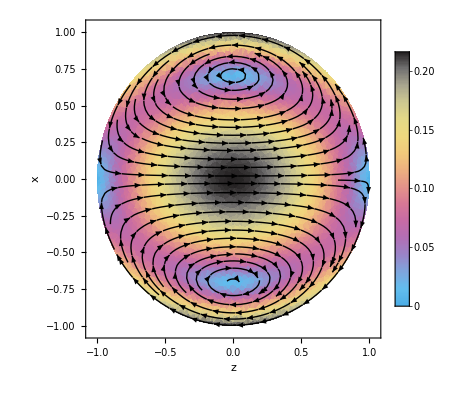

```mathematica
region2=ImplicitRegion[x^2+y^2≤  1&&-2≤ x≤ 2 && -2≤ y≤ 2,{x,y}];
p2SP=StreamPlot[Which[x^2+y^2≤ 1,{vxi,vyi}],{x,y}∈region2,Frame->True,LabelStyle->Directive[FontFamily-> Times,Black,FontSize->16],StreamStyle->Black,FrameLabel->{"z","x"},StreamPoints->15];
p2SD=Show[StreamDensityPlot[{vxi/1,vyi/1},{x,y}∈region2,PlotLegends->Automatic,LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->16],ColorFunction->"CMYKColors",StreamStyle->Black,FrameLabel->{"z","x"},StreamPoints->25]]
```

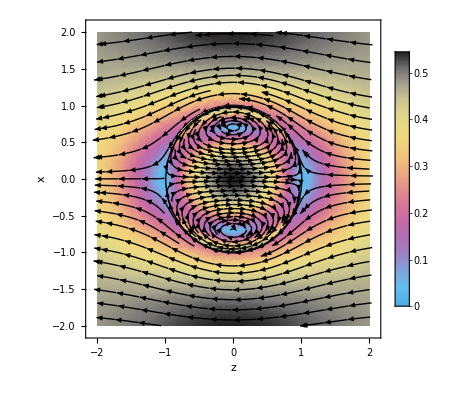

```mathematica
p1=Show[{p1SD}];
p2=Show[{p2SD}];
p3=Graphics[{Thick,Circle[]}];
fig2=Show[{p1,p2,p3}]
```

```mathematica
Export["MaT1S05.png",fig,ImageResolution-> 300]
```

MaT1S05.png

```mathematica
D2=-(378 A2+567 A2 μ+945 B2 μ+32 S^2 μ+126 (α1+β1) Subscript[Ma, T]+126 (3 A2+5 B2) Subscript[Ma, γ])/(126 (3+3 μ+2 Subscript[Ma, γ]))//FullSimplify
```

-(378 A2+567 A2 μ+945 B2 μ+32 S^2 μ+126 (α1+β1) Ma_T+126 (3 A2+5 B2) Ma_γ)/(126 (3+3 μ+2 Ma_γ))

```mathematica
{vxe,vye}=TransformedField["Polar"-> "Cartesian",{ver,veth},{r,θ}-> {x,y}]/.{μ->2,S->0,G-> 1,κ-> 1,Subscript[Ma, T]-> 1,Subscript[Ma, γ]-> 1,R0-> 5};
region1=ImplicitRegion[x^2+y^2≥ 1&&-2≤ x≤ 2 && -2≤ y≤ 2,{x,y}];
p1SP=StreamPlot[Which[x^2+y^2≥1,{vxe,vye}],{x,y}∈region1,Frame->True,LabelStyle->Directive[FontFamily-> Times,Black,FontSize->16],StreamStyle->Black,FrameLabel->{"z","x"},StreamPoints->30];
```

```mathematica
{vxe,vye}=TransformedField["Polar"-> "Cartesian",{ver,veth},{r,θ}-> {x,y}]/.{μ->2,S->0.5,G-> 1,κ-> 1,Subscript[Ma, T]-> 1,Subscript[Ma, γ]-> 1,R0-> 5};
region1=ImplicitRegion[x^2+y^2≥ 1&&-2≤ x≤ 2 && -2≤ y≤ 2,{x,y}];
p1SP2=StreamPlot[Which[x^2+y^2≥1,{vxe,vye}],{x,y}∈region1,Frame->True,LabelStyle->Directive[FontFamily-> Times,Black,FontSize->16],StreamStyle->Red,FrameLabel->{"z","x"},StreamPoints->30];
```

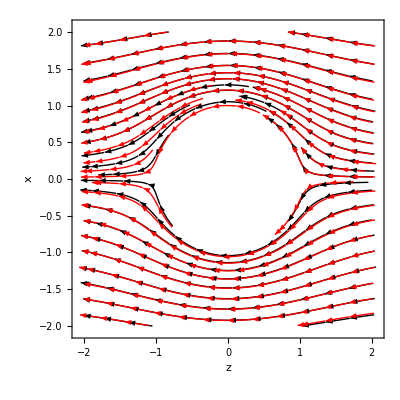

```mathematica
X1=Show[p1SP,p1SP2]
```

```mathematica
{vxi,vyi}=TransformedField["Polar"-> "Cartesian",{vir,vith},{r,θ}-> {x,y}]/.{μ-> 2,S->0,G-> 1,κ-> 1,Subscript[Ma, T]-> 1,Subscript[Ma, γ]-> 1,R0-> 5};
region2=ImplicitRegion[x^2+y^2≤  1&&-2≤ x≤ 2 && -2≤ y≤ 2,{x,y}];
p2SP=StreamPlot[Which[x^2+y^2≤ 1,{vxi,vyi}],{x,y}∈region2,Frame->True,LabelStyle->Directive[FontFamily-> Times,Black,FontSize->16],StreamStyle->Black,FrameLabel->{"z","x"},StreamPoints->10];
```

```mathematica
{vxi,vyi}=TransformedField["Polar"-> "Cartesian",{vir,vith},{r,θ}-> {x,y}]/.{μ-> 2,S->0.5,G->1,κ-> 1,Subscript[Ma, T]-> 1,Subscript[Ma, γ]-> 1,R0-> 5};
region2=ImplicitRegion[x^2+y^2≤  1&&-2≤ x≤ 2 && -2≤ y≤ 2,{x,y}];
p2SP2=StreamPlot[Which[x^2+y^2≤ 1,{vxi,vyi}],{x,y}∈region2,Frame->True,LabelStyle->Directive[FontFamily-> Times,Black,FontSize->16],StreamStyle->Red,FrameLabel->{"z","x"},StreamPoints->10];
```

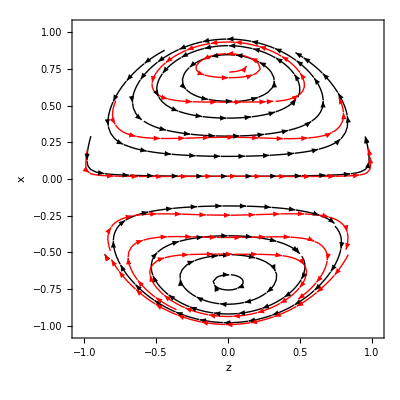

```mathematica
X2=Show[p2SP,p2SP2]
```

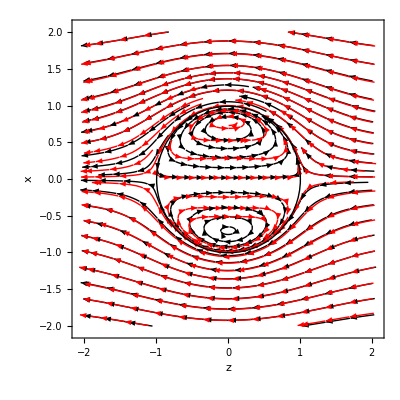

```mathematica
X3=Graphics[{Thick,Circle[]}];
fig=Show[{X1,X2,X3}]
```

```mathematica
Export["streamlines.png",fig,ImageResolution-> 300]
```

streamlines.png

```mathematica
{vxe,vye}=TransformedField["Polar"-> "Cartesian",{ver,veth},{r,θ}-> {x,y}]/.{μ->2,S->0,G-> 1,κ-> 1,Subscript[Ma, T]-> 1,Subscript[Ma, γ]-> 1,R0-> 5};
region1=ImplicitRegion[x^2+y^2≥ 1&&-1.5≤ x≤ 1.5 && 0≤ y≤ 1.5,{x,y}];
p1SPa=StreamPlot[Which[x^2+y^2≥1,{vxe,vye}],{x,y}∈region1,Frame->True,LabelStyle->Directive[FontFamily-> Times,Black,FontSize->16],StreamStyle->Black,FrameLabel->{"z","x"},StreamPoints->15,AspectRatio->1/2];
```

```mathematica
{vxe,vye}=TransformedField["Polar"-> "Cartesian",{ver,veth},{r,θ}-> {x,y}]/.{μ->2,S->0.5,G-> 1,κ-> 1,Subscript[Ma, T]-> 1,Subscript[Ma, γ]-> 1,R0-> 5};
region1=ImplicitRegion[x^2+y^2≥ 1&&-1.5≤ x≤ 1.5 && 0≤ y≤ 1.5,{x,y}];
p1SP2a=StreamPlot[Which[x^2+y^2≥1,{vxe,vye}],{x,y}∈region1,Frame->True,LabelStyle->Directive[FontFamily-> Times,Black,FontSize->16],StreamStyle->Red,FrameLabel->{"z","x"},StreamPoints->15,AspectRatio->1/2];
```

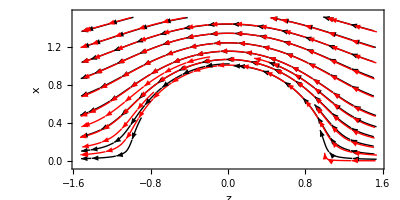

```mathematica
Y1=Show[p1SPa,p1SP2a]
```

```mathematica
{vxi,vyi}=TransformedField["Polar"-> "Cartesian",{vir,vith},{r,θ}-> {x,y}]/.{μ-> 2,S->0,G-> 1,κ-> 1,Subscript[Ma, T]-> 1,Subscript[Ma, γ]-> 1,R0-> 5};
region2=ImplicitRegion[x^2+y^2≤  1&&-1.5≤ x≤ 1.5 && 0≤ y≤ 1.5,{x,y}];
p2SPa=StreamPlot[Which[x^2+y^2≤ 1,{vxi,vyi}],{x,y}∈region2,Frame->True,LabelStyle->Directive[FontFamily-> Times,Black,FontSize->16],StreamStyle->Black,FrameLabel->{"z","x"},StreamPoints->7,AspectRatio->1/2];
```

```mathematica
{vxi,vyi}=TransformedField["Polar"-> "Cartesian",{vir,vith},{r,θ}-> {x,y}]/.{μ-> 2,S->0.5,G->1,κ-> 1,Subscript[Ma, T]-> 1,Subscript[Ma, γ]-> 1,R0-> 5};
region2=ImplicitRegion[x^2+y^2≤  1&&-1.5≤ x≤ 1.5 && 0≤ y≤ 1.5,{x,y}];
p2SP2a=StreamPlot[Which[x^2+y^2≤ 1,{vxi,vyi}],{x,y}∈region2,Frame->True,LabelStyle->Directive[FontFamily-> Times,Black,FontSize->16],StreamStyle->Red,FrameLabel->{"z","x"},StreamPoints->7,AspectRatio->1/2];
```

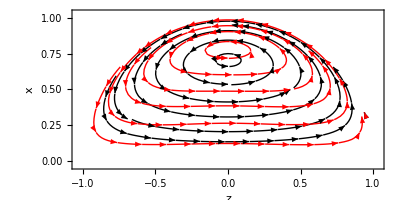

```mathematica
Y2=Show[p2SPa,p2SP2a]
```

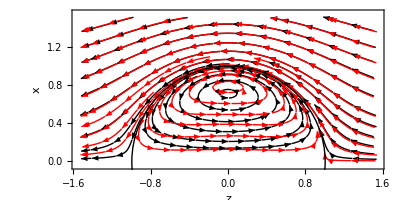

```mathematica
Y3=Graphics[{Thick,Circle[]}];
figX=Show[{Y1,Y2,Y3}]
```

```mathematica
Export["ZoomedStreamlines.png",figX,ImageResolution-> 300]
```

ZoomedStreamlines.png